-1.55304

0.930699

0.952728

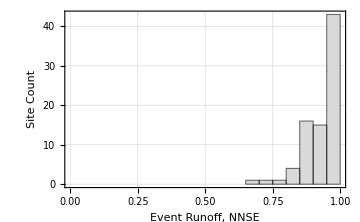

```mathematica
(*Data*)
data[[26]]
data={0.879517846,0.99589051,0.846677543,0.774497781,0.944598133,0.991856988,0.886143572,0.817049833,0.940324579,0.976112435,0.865245996,0.952755192,0.958729575,0.983381608,0.697014961,0.985072988,0.889563261,0.910851517,0.934386748,0.989136108,0.899826257,0.965884203,0.878758991,0.982512366,0.955548923,0.953833436,0.902825969,0.96483477,0.969104362,0.980554327,0.886550116,0.865744123,0.857974585,0.95785146,0.951643416,0.952727891,0.960755686,0.890259115,0.857343328,0.976557689,0.906961494,0.964806802,0.911049028,0.986771272,0.984935069,0.992691297,0.946927559,0.916402603,0.737709183,0.976791714,0.965546211,0.991491002,0.880923021,0.851122802,0.987890335,0.940640014,0.965444004,0.931528115,0.899656097,0.895719148,0.843026315,0.982388161,0.913721955,0.906773153,0.944647911,0.950935407,0.987433112,0.975569109,0.821244681,0.954887817,0.889492683,0.988013299,0.996027276,0.983790068,0.99491118,0.956258859,0.956391917,0.986954963,0.96683427,0.937494791,0.984941974};
Mean[data]
Median[data]
(*Histogram with Styling*)NNSE = Histogram[data,{0,1,0.05},(*Bin width of 0.05 with x-axis from 0 to 1*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, NNSE","Site Count"},PlotRange->{{0,1},Automatic},(*Ensures x-axis stays between 0 and 1*)ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},(*Gray bars with black outlines*)ImageSize->Medium,PlotTheme->"Detailed"]
```

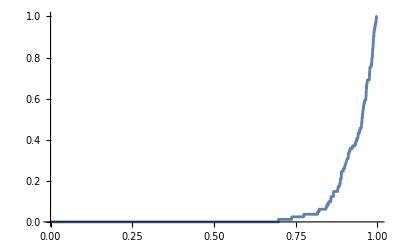

```mathematica
Plot[CDF[EmpiricalDistribution[data],x],{x,0,1},Exclusions->None,PlotRange->All]
```

{12.2053,-11.6463,13.1815,15.7635,-3.84401,-1.46547,6.80965,18.1957,4.5203,-3.93659,6.15307,0.9505,5.7798,-1.83387,13.4587,6.19575,9.59503,0.696923,7.51698,-5.94578,8.08876,2.6223,11.8049,2.04971,3.69644,-1.55304,9.99965,8.66669,-4.18828,-0.189815,10.5436,14.276,12.1552,7.50441,0.490617,8.46356,3.70008,9.29093,18.9676,-0.796143,0.865207,5.78315,10.2693,3.61343,5.07116,-11.551,5.20992,-12.4664,13.1744,-4.00769,0.0783657,-3.26206,3.11521,6.37421,3.331,8.0693,-1.87024,10.1919,-0.356749,-0.134287,6.02493,-6.39325,8.85712,13.8649,-10.2602,6.64443,-7.20484,-0.807766,17.5055,2.6858,5.71681,-2.7053,-5.2473,-16.7086,-6.14652,3.11951,-7.35367,2.93008,-13.5952,4.32311,-1.70998}

-1.55304

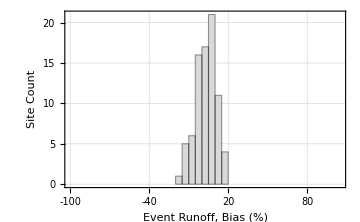

3.61343

3.12323

```mathematica
(*Data*)data={-1.870236709,10.19185335,-0.680211452,-0.134287244,6.024929446,-6.139662946,8.857121061,13.86492331,-7.206791624,6.644432193,-7.204836008,-0.807766334,17.50552417,2.685796865,5.716808769,-2.447049559,-4.311049713,-15.50129797,-0.70034348,3.119513766,6.47581718,2.93008072,-13.59517859,6.588171822,-1.234084981,12.20529923,-11.64634609,13.1815039,15.76354659,-3.844013191,-1.465469468,6.809654985,18.19572769,4.520302514,-3.936592587,6.153072439,0.950500423,5.779804191,-1.83387195,13.45867629,6.195754803,9.595026681,0.696922888,7.516980291,-5.945781069,8.088762855,2.622295647,11.80493953,2.049708338,3.696439265,-1.553035313,9.999647369,8.666691383,-4.188275685,-0.189815011,10.54356069,14.27603898,12.15519581,7.504414687,0.49061718,8.463555174,3.700076235,9.290933224,18.96763519,-0.796143204,13.47048056,5.783153379,10.26933051,3.613433914,5.071156659,-11.12621049,5.209921995,-12.46641546,13.17444785,-4.00768771,0.078365735,-9.187227616,12.7427448,6.374213739,3.330999031,8.069302116};

data = {12.20529923,-11.64634609,13.1815039,15.76354659,-3.844013191,-1.465469468,6.809654985,18.19572769,4.520302514,-3.936592587,6.153072439,0.950500423,5.779804191,-1.83387195,13.45867629,6.195754803,9.595026681,0.696922888,7.516980291,-5.945781069,8.088762855,2.622295647,11.80493953,2.049708338,3.696439265,-1.553035313,9.999647369,8.666691383,-4.188275685,-0.189815011,10.54356069,14.27603898,12.15519581,7.504414687,0.49061718,8.463555174,3.700076235,9.290933224,18.96763519,-0.796143204,0.865207026,5.783153379,10.26933051,3.613433914,5.071156659,-11.55102589,5.209921995,-12.46641546,13.17444785,-4.00768771,0.078365735,-3.262056515,3.115214344,6.374213739,3.330999031,8.069302116,-1.870236709,10.19185335,-0.356748542,-0.134287244,6.024929446,-6.393246813,8.857121061,13.86492331,-10.260209,6.644432193,-7.204836008,-0.807766334,17.50552417,2.685796865,5.716808769,-2.705295137,-5.247299789,-16.70860377,-6.146517467,3.119513766,-7.353667525,2.93008072,-13.59517859,4.323114678,-1.709978491}

data[[26]]
PBIAS=Histogram[data,{Range[-100,105,5]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, Bias (%)","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[-100,100,20],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
data//Median
data//Mean
```

0.108611

1.48764

1.48764

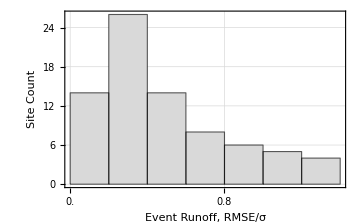

```mathematica
data2={2.586713832,0.333951129,2.665715872,2.907740663,0.216935171,0.290183534,1.766542079,2.975281475,1.155978067,0.523520805,1.374953742,1.133172363,0.985573139,0.477588245,2.819444078,0.427410605,1.596207343,0.777099817,0.643412246,0.352308863,1.876227009,0.882382241,2.06534219,0.324698729,0.961823892,0.551540245,1.784994785,0.645710686,0.426249151,0.70707436,1.988937706,2.294420041,2.459334416,0.667972435,1.41130058,1.352194979,0.763777347,1.788086677,2.409484543,0.577315727,0.629492176,0.762585044,1.348091461,0.376654966,0.400477853,0.397001623,0.947281471,1.395220258,2.087629229,0.581138689,0.473907502,0.304208135,0.849105531,1.091886421,0.352111131,1.116203072,0.647695075,1.31173786,2.187662094,1.005301336,0.924228361,0.34683152,1.557695328,1.714970506,0.559246704,0.966920082,0.322252096,0.357257566,2.116226665,0.944883358,2.851221906,0.43247856,0.234778338,0.473907171,0.290646255,0.846915813,0.498261132,0.400518388,0.687487549,0.600303894,0.238727615};
data ={1.293356922,0.166975564,1.332857927,1.45387033,0.276080918,0.145091767,0.883271042,1.487640737,0.577989034,0.261760403,0.687476871,0.566586182,0.49278657,0.238794122,1.409722039,0.213705302,0.798103672,0.388549909,0.321706123,0.176154431,0.938113505,0.44119112,1.032671096,0.162349365,0.480911946,0.24944218,0.892497391,0.322855343,0.213124576,0.35353718,0.994468853,1.147210021,1.229667209,0.333986217,0.70565029,0.676097489,0.381888674,0.894043338,1.204742272,0.288657864,0.323956493,0.381292522,0.674045731,0.188327482,0.200238927,0.199439201,0.473640736,0.697610129,1.043814615,0.290569344,0.236953751,0.108610844,0.412320762,0.54594321,0.176055565,0.558101536,0.323847538,0.65586893,1.131441143,0.502650668,0.46211418,0.188297566,0.778847664,0.857485253,0.281431174,0.483460041,0.161126048,0.178628783,1.058113333,0.472441679,1.425610949,0.225573262,0.123943698,0.225219774,0.142092934,0.423457906,0.284474894,0.200259194,0.34374366,0.305600215,0.141750889};
Min[data]
Max[data]
Max[data]
NRMSE=Histogram[data,{Range[0,1.5,.2]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, RMSE/σ ","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[0,3.2,.2],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

```mathematica
(*https://journals.ametsoc.org/view/journals/hydr/19/11/jhm-d-18-0139_1.xml#:~:text=VIC%20model%20consists%20of%20two%20modes:%20a,for%20both%20water%20and%20energy%20balance%20simulations.*)
```

```mathematica
Range[-.4,.5,.1]
```

```mathematica
{-0.4,-0.30000000000000004,-0.2,-0.09999999999999998,0.,0.09999999999999998,0.20000000000000007,0.30000000000000004,0.4,0.5}
```

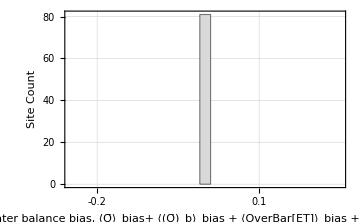

```mathematica
zerosList=ConstantArray[0,81];
RBias=Histogram[zerosList,{Range[-.25,.25,.02]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Water balance bias, ⟨Q̄⟩_bias+ ⟨(Q̄)_b⟩_bias + ⟨OverBar[ET]⟩_bias +σ_(Q̄)^2l_bias","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[-.5,.5,.1],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

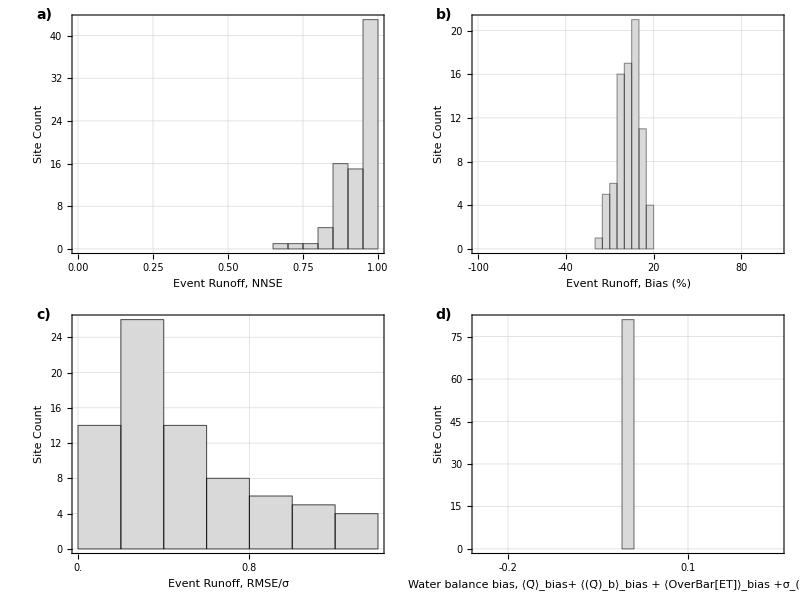

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]

(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[NNSE,"a)"],labeledPlot[PBIAS,"b)"]},{labeledPlot[NRMSE,"c)"],labeledPlot[RBias,"d)"]}},Spacings->2]
```

```mathematica
(*Export the grid as EPS*)Export["Figure8.eps",grid]
```

Fig.X.1.eps

## Parameter Value

```mathematica
Length[data]
```

81

Median 481.352

Average 845.868

84.2099

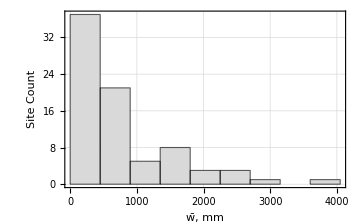

```mathematica
data={77.50200982,79.26752627,12.66547154,64.8394255,40.57131307,50.10582131,109.5921323,37.13530173,69.8968954,40.4100218,46.70455321,19.28119662,14.41857619,23.97558489,20.36234966,15.99376691,29.75090357,36.86763234,27.72706549,186.2462098,407.2844888,42.50013434,19.24323025,50.81444449,31.51563412,224.2720745,282.2716953,154.1837391,52.68052743,50.36359378,160.879482,191.8019465,28.75673007,61.44821615,90.93588126,37.72242376,95.89564738,41.38469905,32.44006926,40.26687443,48.13524223,42.55372055,40.69536355,28.53354565,226.7311307,172.199242,141.8601759,149.7394955,46.07813776,92.89814179,153.1630393,438.5937888,150.5219794,153.6221111,225.8118772,78.58332266,73.60234549,102.2641641,52.66178914,362.0484201,26.74673559,35.88992682,67.10964834,43.09824,63.20017735,85.21548876,32.46020783,22.34249432,254.0362961,35.8840616,54.96036261,47.59665575,10.14557009,39.04274258,15.71522476,12.02476026,8.420993795,54.08279229,12.48122305,29.84578493,20.96169718}*10;

Print["Median "<>ToString[Median[data]]]
Print["Average "<>ToString[Mean[data]]]
Min[data]

wParam=Histogram[data,{Range[0,Max[data],15*30]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"w̄, mm","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

```mathematica
Max[data]
```

5276.74

```mathematica
data2[[26]]
```

3.99565

Median 0.241078

Average 0.411303

0.0558513

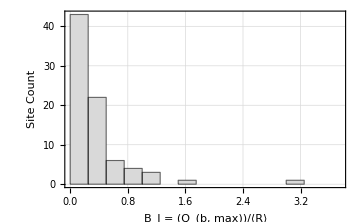

```mathematica
data2={0.212595906,0.170979941,0.302450392,0.136098285,0.241777435,0.217917482,0.208076207,0.126444311,0.208298851,0.223366839,0.127733781,0.134214758,0.055851258,0.241078422,0.547771306,0.259542306,0.316036846,0.352990359,0.245797882,0.328383024,0.340799641,0.331332934,1.09986644,0.140196137,0.074460773,0.12847827,0.14928467,0.095860981,0.524736782,3.046397183,0.080045351,0.204188232,0.19097066,0.143947298,0.140388033,0.352130449,0.134048522,0.148335894,0.214936297,0.059387431,0.325485986,0.437629082,0.840438296,0.54951662,0.221216661,0.293200879,0.164839442,0.372837841,1.13101953,0.302624976,3.995650738,0.11808135,0.059088826,0.912895676,0.778393064,0.624168069,0.320851267,0.374461255,0.164711982,0.1490766,0.223829377,0.213755796,0.130166681,0.108001445,0.16748039,0.439089896,0.263715272,0.252745755,0.110062739,0.261633358,0.381682362,0.222164807,0.493113597,0.298164957,0.996534578,1.525663965,0.697191513,1.168682649,0.594058895,0.191838649,0.182544007};
Print["Median "<>ToString[Median[data2]]]
Print["Average "<>ToString[Mean[data2]]]
Min[data2]

BIParam=Histogram[data2,{Range[0,Max[data2],.25]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"B_I = (Q_(b, max))/⟨R⟩","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

```mathematica
data3[[26]]
```

0.00408597

Median 0.0102656

Average 0.0397004

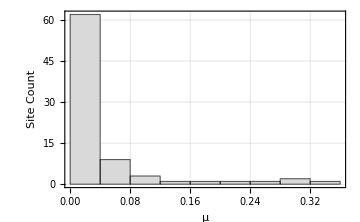

```mathematica
data3={0.011435894,0.013277539,0.009676385,0.010082842,0.015576272,0.008151152,0.007220048,0.070922148,0.005942497,0.008116841,0.01334017,0.00643074,0.01992682,0.011451881,0.023177074,0.020546026,0.007934023,0.003996496,0.006126844,0.003844027,0.003329309,0.000984355,0.001053708,0.011612902,0.001561031,0.000978613,0.000443343,0.017133036,0.005344872,0.00137476,0.001289923,0.002216942,0.003465164,0.019133944,0.005796582,0.046723064,0.036378103,0.020912713,0.057087173,0.005912994,0.002196447,0.052355408,0.069862367,0.002607133,0.020387124,0.063992545,0.009599656,0.237299605,0.003573183,0.106035143,0.004407384,0.011989492,0.001433572,0.010986829,0.027737319,0.132227553,0.002411969,0.003207308,0.314100981,0.011929427,0.001720204,0.007022336,0.002848183,0.022336228,0.00926968,0.078724289,0.012092918,0.004743034,0.314133452,0.112044249,0.352321713,0.187346785,0.082018977,0.052792369,0.074231854,0.000340397,0.001589565,0.01482642,0.262696206,0.010265633,0.004120692};
Print["Median "<>ToString[Median[data3]]]
Print["Average "<>ToString[Mean[data3]]]
μParam=Histogram[data3,{Range[0,Max[data3]+.01,.01*4]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"μ","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

Part::partd: Part specification data4⟦26⟧ is longer than depth of object.

data4⟦26⟧

Median 0.1

Average 0.229136

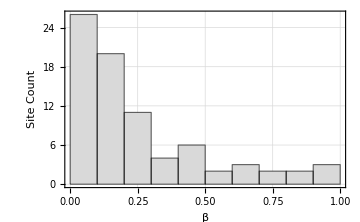

```mathematica
data4[[26]]
data4={0.2,0.01,1,0.1,0.4,0.7,0.1,0.01,0.1,0.01,0.1,0.2,0.01,0.01,0.9,0.4,0.8,1,0.6,0.1,0.4,0.01,0.6,0.1,0.4,0.1,0.2,0.01,0.1,0.4,0.1,0.01,0.01,0.01,0.1,0.01,0.1,0.01,0.1,0.2,0.01,0.2,0.3,0.01,0.2,0.2,0.1,0.2,0.1,0.3,0.2,0.1,0.01,0.1,0.1,0.3,0.2,0.3,0.01,0.1,0.01,0.01,0.1,0.01,0.2,0.9,0.01,0.01,0.01,0.01,0.9,0.1,0.8,0.4,0.6,0.5,0.5,0.7,0.01,0.01,0.01};

Print["Median "<>ToString[Median[data4]]]
Print["Average "<>ToString[Mean[data4]]]
βParam=Histogram[data4,{Range[0,Max[data4]*1.05,.1]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"β","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

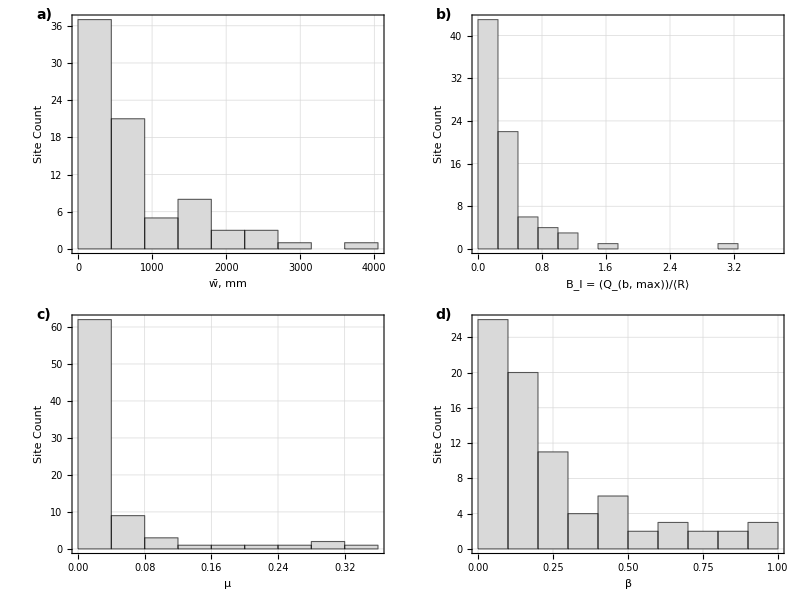

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]
(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[wParam,"a)"],labeledPlot[BIParam,"b)"]},{labeledPlot[μParam,"c)"],labeledPlot[βParam,"d)"]}},Spacings->2]
```

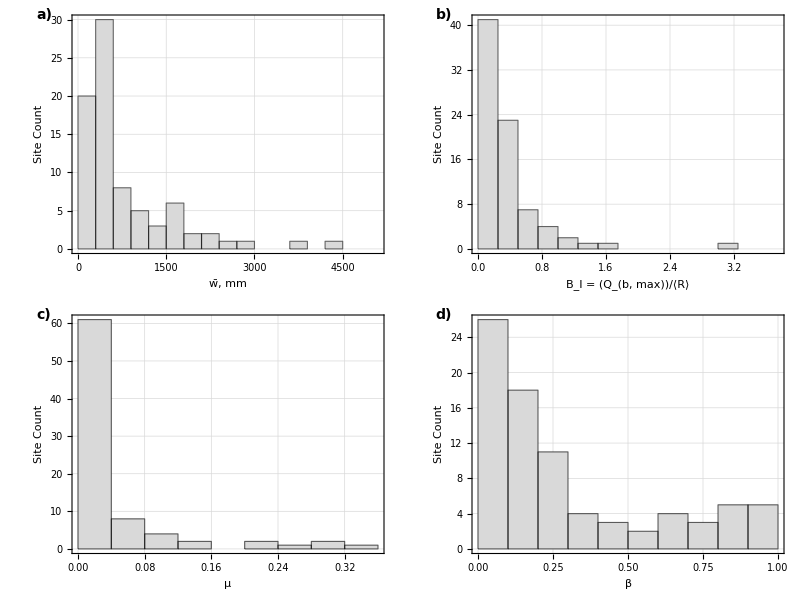

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]

(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[wParam,"a)"],labeledPlot[BIParam,"b)"]},{labeledPlot[μParam,"c)"],labeledPlot[βParam,"d)"]}},Spacings->2]
```

```mathematica
Clear[pz,pzm,χPDF,χIavgN1,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,pχ,CC1N,ϑ]
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
(*χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)

χIavgN1[DI_?NumericQ,γ_?NumericQ]:=χIavgN1[DI,γ]=UnitStep[χIavg[DI,γ]-1]+UnitStep[1-χIavg[DI,γ]]χIavg[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
(*ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]*)
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI/(γs^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI/(γs^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI/γs^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI/γs)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI/γs)-LI/γs ξ10n,0],β==1}}]
(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γs,β,ϑ]=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Take the LOg and then exp to avoid a really small number in the denominator beyond the precision of the computer*)
CC1N[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1N[LI,γs,β,ϑ]=Exp[Evaluate[Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]]]]
pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γs,β,ϑ]=CC1[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
pχPlot[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))]+Log[(1-x)^((γs (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γs/LI))]+Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]],-700]]]
(**)
χavg[LI_,γs_,β_,ϑ_]:=γs/(γs+LI(1+γs(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+2+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
```

```mathematica
800/20
```

40

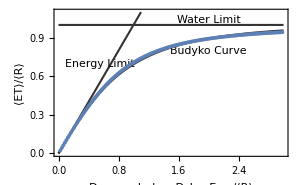

```mathematica
BudykoCurve1 = Table[{DI,DI χIavgN1[DI,γs μ]+ DI aPET[DI,γs μ] χavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]]}/.{γs->40, β->.25,BI->1,μ->.075},{DI,.025,3,.02}];
pt1=Plot[{Budyko[DI],1,DI},{DI,0,3},PlotRange->{0,1.1},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"⟨ET⟩/⟨R⟩",""},{"Dryness Index, D_I = E_max/⟨R⟩",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False];
(*New Value because of Climate shift*)
Label1=Graphics[{Text[Style["Budyko Curve",11,Background->None],{2,.8},{0,0},{1,.15}],Text[Style["Water Limit",11,Background->None],{2,1.04},{0,0},{1,0}],Text[Style["Energy Limit",11,Background->None],{.55,.7},{0,0},{1,2.75}]}];
FigAppendix2=Show[pt1,Label1,ListPlot[BudykoCurve1 ]]
```

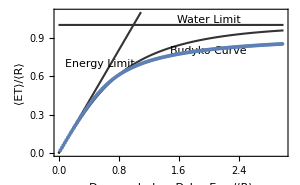

```mathematica
BudykoCurve1 = Table[{DI,DI χIavgN1[DI,γs μ]+ DI aPET[DI,γs μ] χavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]]}/.{γs->460/20, β->.1,BI->.25,μ->.012},{DI,.025,3,.02}];
pt1=Plot[{Budyko[DI],1,DI},{DI,0,3},PlotRange->{0,1.1},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"⟨ET⟩/⟨R⟩",""},{"Dryness Index, D_I = E_max/⟨R⟩",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False];
(*New Value because of Climate shift*)
Label1=Graphics[{Text[Style["Budyko Curve",11,Background->None],{2,.8},{0,0},{1,.15}],Text[Style["Water Limit",11,Background->None],{2,1.04},{0,0},{1,0}],Text[Style["Energy Limit",11,Background->None],{.55,.7},{0,0},{1,2.75}]}];
FigAppendix2=Show[pt1,Label1,ListPlot[BudykoCurve1 ]]
```